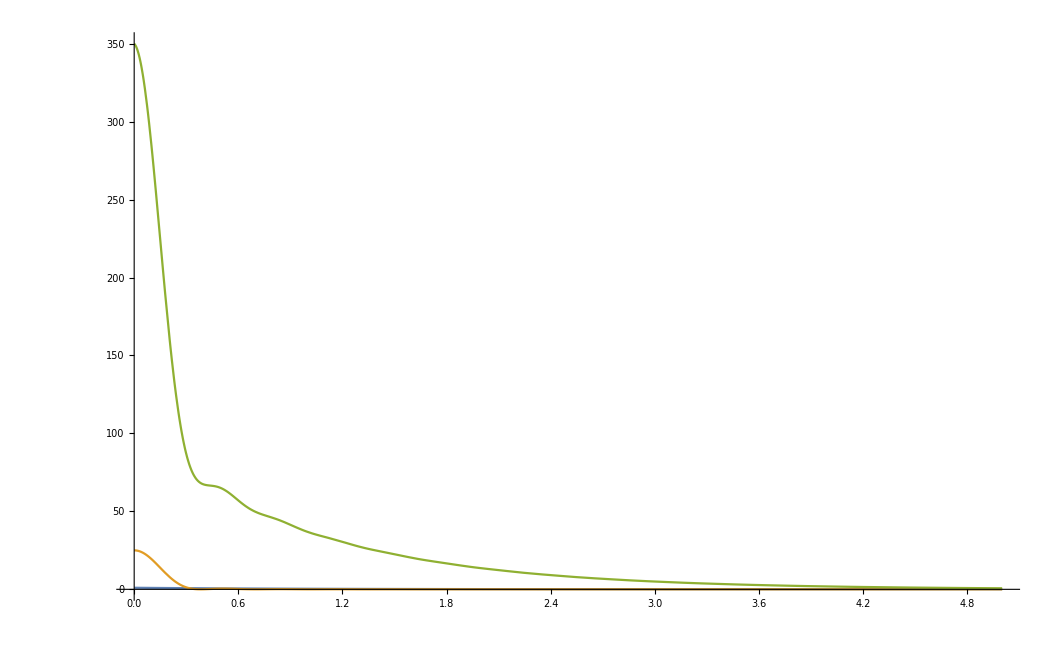

```mathematica
Plot[{Exp[-x],BesselJ[1,10x]^2/x^2,100*Exp[-x]+10*BesselJ[1,10x]^2/x^2},{x,0,5},PlotRange->Full]
```

```mathematica
f[x_]:=100*Exp[-x]+10*BesselJ[1,10x]^2/x^2
f'[x]
Limit[f'[t],t->0]
```

-100 ⅇ^-x-(20 BesselJ[1,10 x]^2)/x^3+(100 BesselJ[1,10 x] (BesselJ[0,10 x]-BesselJ[2,10 x]))/x^2

-100

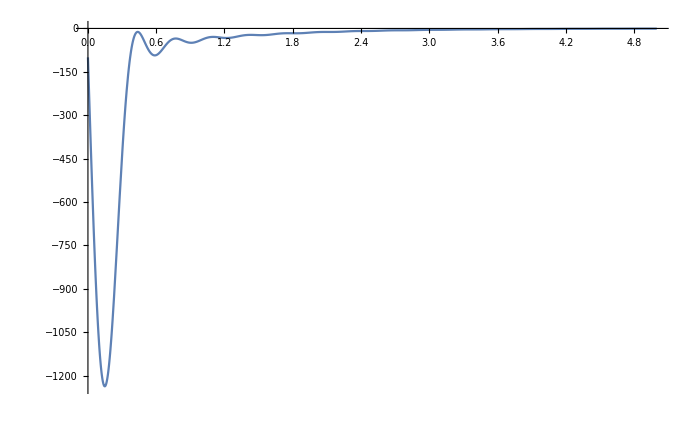

```mathematica
Plot[-100 ⅇ^-x-(20 BesselJ[1,10 x]^2)/x^3+(100 BesselJ[1,10 x] (BesselJ[0,10 x]-BesselJ[2,10 x]))/x^2,{x,0,5},PlotRange->All]
```

```mathematica
FindMaximum[{10*BesselJ[1,10x]^2/x^2,x>0.1},{x,0.1}]
```

{193.645,{x→0.1}}